# Cavity Equilibria

## Parameters

```mathematica
ℏ = 6.626*^-34 /(2Pi)
```

1.05456×10^-34

```mathematica
ϵ0 = 8.854*^-12
```

8.854×10^-12

```mathematica
c = 2.991*^8
```

2.991×10^8

```mathematica
λ0 = 1550*^-9
```

31/20000000

```mathematica
k0=2*Pi/λ0
```

(40000000 π)/31

```mathematica
ω0 = c*k0
```

1.21245×10^15

```mathematica
Pt = 0.5
```

0.5

```mathematica
Wt=1*^-6
```

1/1000000

```mathematica
zR = Pi*Wt^2/λ0
```

π/1550000

```mathematica
E0 = Sqrt[(4*Pt)/(Pi*ϵ0*c*Wt^2)]
```

1.55047×10^7

```mathematica
ρ = 2200
```

2200

```mathematica
ϵ=2.07
```

2.07

```mathematica
R = 100*^-9
```

1/10000000

```mathematica
V = 4/3 * Pi * R^3
```

π/750000000000000000000

```mathematica
α= 3*V*ϵ0* (ϵ-1)/(ϵ+2)
```

2.92509×10^-32

```mathematica
Wc = 20*^-6
```

1/50000

```mathematica
Lc=19.8*^-3
```

0.0198

```mathematica
Vc = Pi*Wc^2*Lc/4
```

6.22035×10^-12

```mathematica
m  =ρ*V
```

(11 π)/3750000000000000000

```mathematica
κ=18*^4 *2Pi
```

360000 π

```mathematica
ϕ := 0
```

## System-Functions

```mathematica
E0c[Δ_] := Sqrt[ℏ*(Δ+ω0)/(2ϵ0*Vc)]
```

```mathematica
Ec[x_,y_, z_, Δ_] :=E0c[Δ]*Exp[-(x^2+z^2)/Wc^2]*Cos[(Δ+ω0)/c * y]
```

```mathematica
ϕt[x_, y_, z_]:=-ArcTan[z/zR]+k0*z/2 * (x^2+y^2)/(z^2+zR^2)
```

```mathematica
W[z_]:=Wt*Sqrt[1+(z/zR)^2]
```

```mathematica
Et[x_, y_, z_]:=E0/2 * Exp[I*(k0*z+ϕt[x,y,z])]*Wt/W[z]*Exp[-(y/W[z])^2]*Exp[-(x/W[z])^2]
```

```mathematica
l[Δ_]:=λ0*(1-Δ/ω0)
```

```mathematica
δc[z1_, z2_, Δ_]:=Δ - α/ℏ * (Ec[0, -l[Δ]/2, z1, Δ]^2 + Ec[0, l[Δ]/2, z2, Δ]^2)
```

```mathematica
αceq[z1_, z2_,Δ_] := 
α/ℏ *(
Ec[0, -l[Δ]/2, z1, Δ]*Et[0,0,z1]+
Ec[0, l[Δ]/2, z2, Δ]*Et[0,0, z2]*Exp[I*ϕ]
)/(δc[z1, z2, Δ]-I*κ/2)
```

```mathematica
F[z1_, z2_, Δ_]:={
Re[(Conjugate[αceq[z1, z2,Δ]]*Ec[0, -l[Δ]/2, z1, Δ]+Conjugate[Et[0,0, z1]])*
(αceq[z1, z2, Δ]*(-2*z1/Wc^2)*Ec[0, -l[Δ]/2, z1, Δ]+(I*(k0-zR/(z1^2+zR^2))-z1/(z1^2+zR^2))*Et[0,0, z1])],
Re[(Conjugate[αceq[z1, z2,Δ]]*Ec[0, +l[Δ]/2, z2, Δ]+Conjugate[Et[0,0, z2]]*Exp[-I*ϕ])*
(αceq[z1, z2, Δ]*(-2*z2/Wc^2)*Ec[0, +l[Δ]/2, z2, Δ]+(I*(k0-zR/(z2^2+zR^2))-z2/(z2^2+zR^2))*Et[0,0, z2]*Exp[I*ϕ])]
}
```

## Plotting

## For thesis

```mathematica
Δ = 387.91*2000*Pi
```

2.43731×10^6

```mathematica
NPoints = 100;
CenterPoint = {0.5,-20};
Dims = {2,2};
Leftlim = CenterPoint[[1]]-Dims[[1]]/2;
Rightlim = CenterPoint[[1]]+Dims[[1]]/2; 
Toplim = CenterPoint[[2]]+Dims[[2]]/2; 
Bottomlim = CenterPoint[[2]]-Dims[[1]]/2; 
Data = ParallelTable[Flatten@{{z1,z2},Norm@F[z1/10^6, z2/10^6,Δ]},{z1,Subdivide[Leftlim, Rightlim,NPoints]},{z2,Subdivide[Bottomlim, Toplim,NPoints]}];
(*Data2 = ParallelTable[{{z1,z2},F[z1/10^6, z2/10^6, 100*2000*Pi]},{z1,Subdivide[Leftlim, Rightlim,NPoints]},{z2,Subdivide[Bottomlim, Toplim,NPoints]}];*)
```

```mathematica
PlotData = Flatten[Data,1];
(*StreamPlotData = Flatten[Data2,1];*)
```

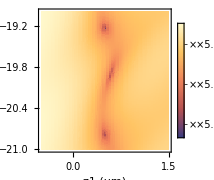

```mathematica
ListDensityPlot[PlotData,  ScalingFunctions->{None,None, "Log"},PlotRange->{Full,Full,{Automatic, Automatic}}, ClippingStyle->Automatic,PlotLegends->BarLegend[Automatic, ScalingFunctions->"Log"],InterpolationOrder->0, FrameLabel->{"z1 (μm)", "z2 (μm)"}, ImageSize->Small]
```

```mathematica
Export[FileNameJoin[NotebookDirectory[], "OnAxes.svg"], ]
```

/home/percy/Downloads/OnAxes.svg

```mathematica
NPoints = 100;
CenterPoint = {20,12};
Dims = {2,2};
Leftlim = CenterPoint[[1]]-Dims[[1]]/2;
Rightlim = CenterPoint[[1]]+Dims[[1]]/2; 
Toplim = CenterPoint[[2]]+Dims[[2]]/2; 
Bottomlim = CenterPoint[[2]]-Dims[[1]]/2; 
Data = ParallelTable[Flatten@{{z1,z2},Norm@F[z1/10^6, z2/10^6, Δ]},{z1,Subdivide[Leftlim, Rightlim,NPoints]},{z2,Subdivide[Bottomlim, Toplim,NPoints]}];
(*Data2 = ParallelTable[{{z1,z2},F[z1/10^6, z2/10^6, 100*2000*Pi]},{z1,Subdivide[Leftlim, Rightlim,NPoints]},{z2,Subdivide[Bottomlim, Toplim,NPoints]}];*)
```

```mathematica
PlotData = Flatten[Data,1];
(*StreamPlotData = Flatten[Data2,1];*)
```

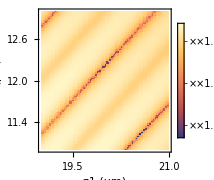

```mathematica
ListDensityPlot[PlotData,  ScalingFunctions->{None,None, "Log"},PlotRange->{Full,Full,{10^13, Automatic}}, ClippingStyle->Automatic,PlotLegends->BarLegend[Automatic, ScalingFunctions->"Log"],InterpolationOrder->0, FrameLabel->{"z1 (μm)", "z2 (μm)"}, ImageSize->Small]
```

```mathematica
Export[FileNameJoin[NotebookDirectory[], "PlusPlusSector.svg"], ]
```

/home/percy/Downloads/PlusPlusSector.svg

```mathematica
NPoints = 100;
CenterPoint = {19,-20.5};
Dims = {2,2};
Leftlim = CenterPoint[[1]]-Dims[[1]]/2;
Rightlim = CenterPoint[[1]]+Dims[[1]]/2; 
Toplim = CenterPoint[[2]]+Dims[[2]]/2; 
Bottomlim = CenterPoint[[2]]-Dims[[1]]/2; 
Data = ParallelTable[Flatten@{{z1,z2},Norm@F[z1/10^6, z2/10^6,  Δ]},{z1,Subdivide[Leftlim, Rightlim,NPoints]},{z2,Subdivide[Bottomlim, Toplim,NPoints]}];
(*Data2 = ParallelTable[{{z1,z2},F[z1/10^6, z2/10^6, 100*2000*Pi]},{z1,Subdivide[Leftlim, Rightlim,NPoints]},{z2,Subdivide[Bottomlim, Toplim,NPoints]}];*)
```

```mathematica
PlotData = Flatten[Data,1];
(*StreamPlotData = Flatten[Data2,1];*)
```

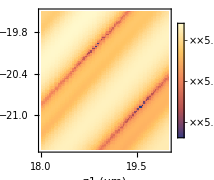

```mathematica
ListDensityPlot[PlotData,  ScalingFunctions->{None,None, "Log"},PlotRange->{Full,Full,{Automatic, Automatic}}, ClippingStyle->Automatic,PlotLegends->BarLegend[Automatic, ScalingFunctions->"Log"],InterpolationOrder->0, FrameLabel->{"z1 (μm)", "z2 (μm)"}, ImageSize->Small]
```

```mathematica
Export[FileNameJoin[NotebookDirectory[], "PlusMinusSector.svg"], ]
```

/home/percy/Downloads/PlusMinusSector.svg